```mathematica
Supply and Demand can be plotted together as below.
```

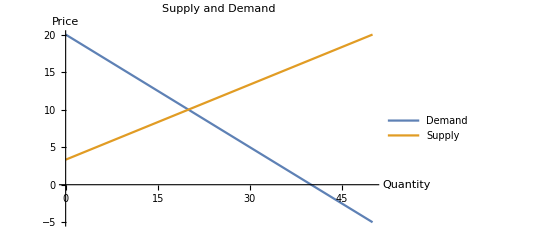

```mathematica
Plot[{-0.5Q+20, 1/3(Q+10)}, {Q, 0, 50},AxesLabel->{"Quantity","Price"},PlotLabel->HoldForm[Supply and Demand],LabelStyle->{GrayLevel[0]},PlotLegends->{"Demand", "Supply"}]
```

```mathematica
Supply and Demand are in equlibrium at the point of intersection of the two lines, this point can be calculated by solving the two simultanious equations for Supply and Demand as shown below:
```

```mathematica
Solve[{-0.5Q+20 == P , 1/3(Q+10) ==P}, {Q, P}]
```

{{Q→20.,P→10.}}